```mathematica
input=Import["/home/leartsura/Documents/projects/aoc23/input"];
```

```mathematica
lines:=StringSplit[input, "\n"]
```

```mathematica
notEmpty[s_]:=s!=""
```

```mathematica
wiring:=Select[notEmpty][StringSplit[#,{":"," "}]]&/@lines
```

```mathematica
G=Flatten[Table[UndirectedEdge[#[[1]],#[[i]]],{i,2,Length[#]}]&/@wiring];
```

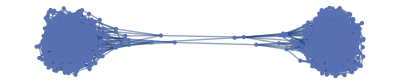

```mathematica
Graph[G]
```

```mathematica
FindEdgeCut[G]
```

{tmt<->pnz,gbc<->hxr,xkz<->mvv}

```mathematica
mincut=FindMinimumCut[G];
```

```mathematica
mincut[[1]]
Apply[Times,Length[#]&/@mincut[[2]]]
```

3

569904